```mathematica
mZ=92000;
```

```mathematica
Gdec[sMD1_,sMD2_,sMZp_,sTtheta_,sEps_,sAlphaX_]:=(5*sAlphaX*sEps^2*sTtheta^2*(-((-sMD1^2+sMD2^2)*(1000*mZ^2+80*(25*sMD1^2-75*sMD1*sMD2+25*sMD2^2-16*mZ^2-50*sMZp^2)-(101*mZ^2*(-sMD1^4-sMD2^4+6*sMD1*sMD2*mZ^2-sMD2^2*mZ^2+2*mZ^4+sMD1^2*(2*sMD2^2-mZ^2)))/(mZ^2-sMZp^2)^2+((961*mZ^4-1860*mZ^2*sMZp^2+1000*sMZp^4)*(sMD1^4+sMD2^4-6*sMD1*sMD2*sMZp^2+sMD2^2*sMZp^2-2*sMZp^4+sMD1^2*(-2*sMD2^2+sMZp^2)))/(-(mZ^2*sMZp)+sMZp^3)^2))-2*(3000*sMD1^3*sMD2-241*mZ^4-280*mZ^2*sMZp^2-3000*sMZp^4+60*sMD1*sMD2*(50*sMD2^2-7*mZ^2-100*sMZp^2)+30*sMD1^2*(7*mZ^2+100*sMZp^2)+30*sMD2^2*(7*mZ^2+100*sMZp^2))*Log[-2*sMD1^2]+2*(3000*sMD1^3*sMD2-241*mZ^4-280*mZ^2*sMZp^2-3000*sMZp^4+60*sMD1*sMD2*(50*sMD2^2-7*mZ^2-100*sMZp^2)+30*sMD1^2*(7*mZ^2+100*sMZp^2)+30*sMD2^2*(7*mZ^2+100*sMZp^2))*Log[-2*sMD1*sMD2]+(2*mZ^2*(-sMD1^2+2*sMD1*sMD2-sMD2^2+mZ^2)*(241*mZ^8-443*mZ^6*sMZp^2-sMD1^6*(31*mZ^2+70*sMZp^2)-2*sMD1^5*sMD2*(31*mZ^2+70*sMZp^2)+sMD1^4*sMD2^2*(31*mZ^2+70*sMZp^2)-sMD2^6*(31*mZ^2+70*sMZp^2)+sMD2^2*(-210*mZ^6+513*mZ^4*sMZp^2)+sMD1^3*sMD2*(-179*mZ^4+583*mZ^2*sMZp^2+4*sMD2^2*(31*mZ^2+70*sMZp^2))-sMD1*sMD2*(62*mZ^6+140*mZ^4*sMZp^2+2*sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(179*mZ^4-583*mZ^2*sMZp^2))+sMD1^2*(-210*mZ^6+513*mZ^4*sMZp^2+sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(-358*mZ^4+1166*mZ^2*sMZp^2)))*Log[-mZ^2])/(Sqrt[sMD1^4+(sMD2^2-mZ^2)^2-2*sMD1^2*(sMD2^2+mZ^2)]*(mZ^2-sMZp^2)^3)-(2*mZ^2*(-sMD1^2+2*sMD1*sMD2-sMD2^2+mZ^2)*(241*mZ^8-443*mZ^6*sMZp^2-sMD1^6*(31*mZ^2+70*sMZp^2)-2*sMD1^5*sMD2*(31*mZ^2+70*sMZp^2)+sMD1^4*sMD2^2*(31*mZ^2+70*sMZp^2)-sMD2^6*(31*mZ^2+70*sMZp^2)+sMD2^2*(-210*mZ^6+513*mZ^4*sMZp^2)+sMD1^3*sMD2*(-179*mZ^4+583*mZ^2*sMZp^2+4*sMD2^2*(31*mZ^2+70*sMZp^2))-sMD1*sMD2*(62*mZ^6+140*mZ^4*sMZp^2+2*sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(179*mZ^4-583*mZ^2*sMZp^2))+sMD1^2*(-210*mZ^6+513*mZ^4*sMZp^2+sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(-358*mZ^4+1166*mZ^2*sMZp^2)))*Log[(sMD1-sMD2)^2-mZ^2])/(Sqrt[sMD1^4+(sMD2^2-mZ^2)^2-2*sMD1^2*(sMD2^2+mZ^2)]*(mZ^2-sMZp^2)^3)+(2*mZ^2*(-sMD1^2+2*sMD1*sMD2-sMD2^2+mZ^2)*(241*mZ^8-443*mZ^6*sMZp^2-sMD1^6*(31*mZ^2+70*sMZp^2)-2*sMD1^5*sMD2*(31*mZ^2+70*sMZp^2)+sMD1^4*sMD2^2*(31*mZ^2+70*sMZp^2)-sMD2^6*(31*mZ^2+70*sMZp^2)+sMD2^2*(-210*mZ^6+513*mZ^4*sMZp^2)+sMD1^3*sMD2*(-179*mZ^4+583*mZ^2*sMZp^2+4*sMD2^2*(31*mZ^2+70*sMZp^2))-sMD1*sMD2*(62*mZ^6+140*mZ^4*sMZp^2+2*sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(179*mZ^4-583*mZ^2*sMZp^2))+sMD1^2*(-210*mZ^6+513*mZ^4*sMZp^2+sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(-358*mZ^4+1166*mZ^2*sMZp^2)))*Log[2*sMD1*sMD2*(sMD1^2-2*sMD1*sMD2+sMD2^2-mZ^2)])/(Sqrt[sMD1^4+(sMD2^2-mZ^2)^2-2*sMD1^2*(sMD2^2+mZ^2)]*(mZ^2-sMZp^2)^3)-(2*mZ^2*(-sMD1^2+2*sMD1*sMD2-sMD2^2+mZ^2)*(241*mZ^8-443*mZ^6*sMZp^2-sMD1^6*(31*mZ^2+70*sMZp^2)-2*sMD1^5*sMD2*(31*mZ^2+70*sMZp^2)+sMD1^4*sMD2^2*(31*mZ^2+70*sMZp^2)-sMD2^6*(31*mZ^2+70*sMZp^2)+sMD2^2*(-210*mZ^6+513*mZ^4*sMZp^2)+sMD1^3*sMD2*(-179*mZ^4+583*mZ^2*sMZp^2+4*sMD2^2*(31*mZ^2+70*sMZp^2))-sMD1*sMD2*(62*mZ^6+140*mZ^4*sMZp^2+2*sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(179*mZ^4-583*mZ^2*sMZp^2))+sMD1^2*(-210*mZ^6+513*mZ^4*sMZp^2+sMD2^4*(31*mZ^2+70*sMZp^2)+sMD2^2*(-358*mZ^4+1166*mZ^2*sMZp^2)))*Log[sMD1^4+sMD2^4-sMD2^2*mZ^2-sMD1^2*(2*sMD2^2+mZ^2)+(-sMD1^2+sMD2^2)*Sqrt[sMD1^4+(sMD2^2-mZ^2)^2-2*sMD1^2*(sMD2^2+mZ^2)]])/(Sqrt[sMD1^4+(sMD2^2-mZ^2)^2-2*sMD1^2*(sMD2^2+mZ^2)]*(mZ^2-sMZp^2)^3)+(4*(sMD1^2-2*sMD1*sMD2+sMD2^2-sMZp^2)*(2*sMD1^5*sMD2*mZ^2*(31*mZ^2+70*sMZp^2)-sMD1^4*sMD2^2*mZ^2*(31*mZ^2+70*sMZp^2)+sMD1^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMZp^4*(2883*mZ^6-8401*mZ^4*sMZp^2+8720*mZ^2*sMZp^4-3000*sMZp^6)+sMD2^2*(-2883*mZ^6*sMZp^2+8370*mZ^4*sMZp^4-8790*mZ^2*sMZp^6+3000*sMZp^8)-sMD1^3*sMD2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6+4*sMD2^2*(31*mZ^4+70*mZ^2*sMZp^2))-sMD1^2*(2883*mZ^6*sMZp^2-8370*mZ^4*sMZp^4+8790*mZ^2*sMZp^6-3000*sMZp^8+sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+2*sMD2^2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6))+sMD1*sMD2*(62*mZ^4*sMZp^4+140*mZ^2*sMZp^6+2*sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^2*(-2883*mZ^6+8339*mZ^4*sMZp^2-8860*mZ^2*sMZp^4+3000*sMZp^6)))*Log[sMZp])/((-mZ^2+sMZp^2)^3*Sqrt[sMD1^4+(sMD2^2-sMZp^2)^2-2*sMD1^2*(sMD2^2+sMZp^2)])+(2*(sMD1^2-2*sMD1*sMD2+sMD2^2-sMZp^2)*(2*sMD1^5*sMD2*mZ^2*(31*mZ^2+70*sMZp^2)-sMD1^4*sMD2^2*mZ^2*(31*mZ^2+70*sMZp^2)+sMD1^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMZp^4*(2883*mZ^6-8401*mZ^4*sMZp^2+8720*mZ^2*sMZp^4-3000*sMZp^6)+sMD2^2*(-2883*mZ^6*sMZp^2+8370*mZ^4*sMZp^4-8790*mZ^2*sMZp^6+3000*sMZp^8)-sMD1^3*sMD2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6+4*sMD2^2*(31*mZ^4+70*mZ^2*sMZp^2))-sMD1^2*(2883*mZ^6*sMZp^2-8370*mZ^4*sMZp^4+8790*mZ^2*sMZp^6-3000*sMZp^8+sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+2*sMD2^2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6))+sMD1*sMD2*(62*mZ^4*sMZp^4+140*mZ^2*sMZp^6+2*sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^2*(-2883*mZ^6+8339*mZ^4*sMZp^2-8860*mZ^2*sMZp^4+3000*sMZp^6)))*Log[2*sMD1*sMD2*(sMD1^2-2*sMD1*sMD2+sMD2^2-sMZp^2)])/((-mZ^2+sMZp^2)^3*Sqrt[sMD1^4+(sMD2^2-sMZp^2)^2-2*sMD1^2*(sMD2^2+sMZp^2)])-(2*(sMD1^2-2*sMD1*sMD2+sMD2^2-sMZp^2)*(2*sMD1^5*sMD2*mZ^2*(31*mZ^2+70*sMZp^2)-sMD1^4*sMD2^2*mZ^2*(31*mZ^2+70*sMZp^2)+sMD1^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMZp^4*(2883*mZ^6-8401*mZ^4*sMZp^2+8720*mZ^2*sMZp^4-3000*sMZp^6)+sMD2^2*(-2883*mZ^6*sMZp^2+8370*mZ^4*sMZp^4-8790*mZ^2*sMZp^6+3000*sMZp^8)-sMD1^3*sMD2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6+4*sMD2^2*(31*mZ^4+70*mZ^2*sMZp^2))-sMD1^2*(2883*mZ^6*sMZp^2-8370*mZ^4*sMZp^4+8790*mZ^2*sMZp^6-3000*sMZp^8+sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+2*sMD2^2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6))+sMD1*sMD2*(62*mZ^4*sMZp^4+140*mZ^2*sMZp^6+2*sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^2*(-2883*mZ^6+8339*mZ^4*sMZp^2-8860*mZ^2*sMZp^4+3000*sMZp^6)))*Log[-(sMD1-sMD2)^2+sMZp^2])/((-mZ^2+sMZp^2)^3*Sqrt[sMD1^4+(sMD2^2-sMZp^2)^2-2*sMD1^2*(sMD2^2+sMZp^2)])-(2*(sMD1^2-2*sMD1*sMD2+sMD2^2-sMZp^2)*(2*sMD1^5*sMD2*mZ^2*(31*mZ^2+70*sMZp^2)-sMD1^4*sMD2^2*mZ^2*(31*mZ^2+70*sMZp^2)+sMD1^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^6*(31*mZ^4+70*mZ^2*sMZp^2)+sMZp^4*(2883*mZ^6-8401*mZ^4*sMZp^2+8720*mZ^2*sMZp^4-3000*sMZp^6)+sMD2^2*(-2883*mZ^6*sMZp^2+8370*mZ^4*sMZp^4-8790*mZ^2*sMZp^6+3000*sMZp^8)-sMD1^3*sMD2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6+4*sMD2^2*(31*mZ^4+70*mZ^2*sMZp^2))-sMD1^2*(2883*mZ^6*sMZp^2-8370*mZ^4*sMZp^4+8790*mZ^2*sMZp^6-3000*sMZp^8+sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+2*sMD2^2*(2883*mZ^6-8339*mZ^4*sMZp^2+8860*mZ^2*sMZp^4-3000*sMZp^6))+sMD1*sMD2*(62*mZ^4*sMZp^4+140*mZ^2*sMZp^6+2*sMD2^4*(31*mZ^4+70*mZ^2*sMZp^2)+sMD2^2*(-2883*mZ^6+8339*mZ^4*sMZp^2-8860*mZ^2*sMZp^4+3000*sMZp^6)))*Log[sMD1^4+sMD2^4-sMD2^2*sMZp^2-sMD1^2*(2*sMD2^2+sMZp^2)+(-sMD1^2+sMD2^2)*Sqrt[sMD1^4+(sMD2^2-sMZp^2)^2-2*sMD1^2*(sMD2^2+sMZp^2)]])/((-mZ^2+sMZp^2)^3*Sqrt[sMD1^4+(sMD2^2-sMZp^2)^2-2*sMD1^2*(sMD2^2+sMZp^2)])))/(7.374714 10^6*sMD2^3*π)
```

```mathematica
Gdec[100,101.,400,10^-5,10^-4,1]
```

-2.81139×10^-23+0. ⅈ

```mathematica
Gdec[100,101,400,10^-5,10^-4,1]
```

0.+0. ⅈ

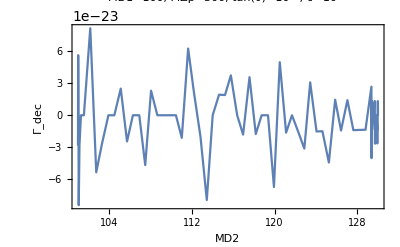

```mathematica
Plot[Re[Gdec[100,MD2,300,10^-5,10^-4,1]],{MD2,101,130},Frame->True,FrameLabel->{"MD2","Γ_dec"},PlotLabel->"MD1=100, MZp=300, tan(θ)=10^-5, ϵ=10^-4"]
```

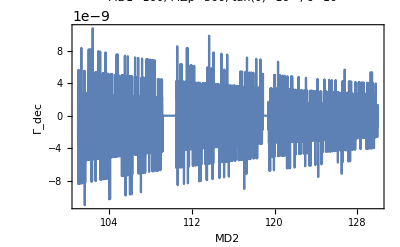

```mathematica
Plot[Re[Gdec[100,MD2,300,10^-1,10^-1,1]],{MD2,101,130},Frame->True,FrameLabel->{"MD2","Γ_dec"},PlotLabel->"MD1=100, MZp=300, tan(θ)=10^-1, ϵ=10^-1"]
```